# FractionalDTimeSeries

Calculate the fractional derivative of a time series

## Definition

```mathematica
FractionalDTimeSeries::tol="Argument `1` generates more weights than total data points in the time series. Please, increase it.";
```

```mathematica
FractionalDTimeSeries[ts_TemporalData,d_?NonNegative,t:_?Positive:0.0001 ]:=Module[
{timeSeries=ts,diffOrder=d,tolerance=t,fdSeries,idxDiff,check,k,timeSeriesValues,totalWeights,weights},
weights=Reverse[NestWhileList[k=0;
(-#*((diffOrder-k+1)/k))& ,1,( k++;Abs[#]>tolerance)&,
1, ∞, -1]];
totalWeights=Length[weights];
timeSeriesValues=QuantityMagnitude@timeSeries["Values"];
check=(Length[timeSeriesValues]>=totalWeights);
(idxDiff=Range[totalWeights,Length[timeSeriesValues]];
fdSeries=(weights.timeSeriesValues[[#[[1]];;#[[2]]]])&/@Transpose[{Range[Length[idxDiff]], idxDiff}];
TimeSeries[fdSeries,{timeSeries["Dates"][[totalWeights;;]]},TemporalRegularity->True])/;If[check,True,ResourceFunction["ResourceFunctionMessage"][FractionalDTimeSeries::tol,t];False]]
```

## Documentation

### Usage

FractionalDTimeSeries[tseries,d]

applies a fractional derivative of order d to the time series tseries.

FractionalDTimeSeries[tseries,d,tol]

uses tolerance value tol for memory preservation.

### Details & Options

FractionalDTimeSeries[tseries,d,tol] represents a fractional difference operator of order d for the time series tseries, given a tolerance tol, as formulated by Marcos Lopez de Prado (2018).

The order d should be a positive real.

By default, the tolerance is set to 0.0001.

## Examples

### Basic Examples

Get a time series of prices and visualize it:

```mathematica
ts = FinancialData["GE","Close","Jan. 1, 2010"]
```

TimeSeries[…]

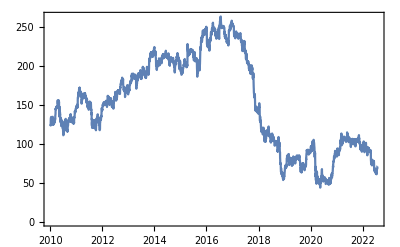

```mathematica
DateListPlot@ts
```

Compute the half difference of the time series and visualize it:

```mathematica
fdseries=FractionalDTimeSeries[ts, 0.5]
```

TimeSeries[…]

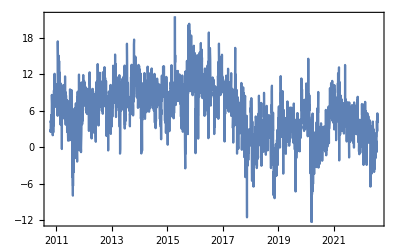

```mathematica
DateListPlot@fdseries
```

### Scope

Get a time series of prices:

```mathematica
ts = FinancialData["TEVA","Close","Jan. 1, 2010"]
```

TimeSeries[…]

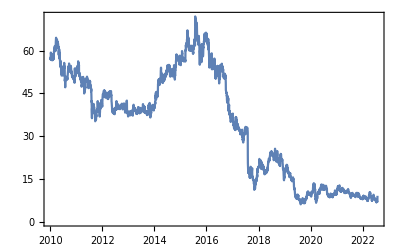

```mathematica
DateListPlot@ts
```

Computing the FractionalDTimeSeries of order 1 leads to the usual first difference:

```mathematica
firstDiff = FractionalDTimeSeries[ts, 1]
```

TimeSeries[…]

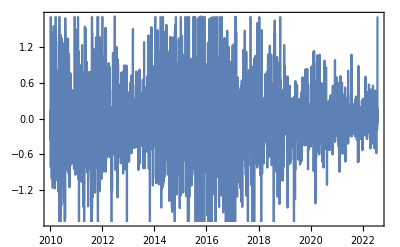

```mathematica
DateListPlot@firstDiff
```

However, applying the half-difference twice on the original time series yields an equivalent first difference, but with fewer data points and on a slightly different scale:

```mathematica
doublefdseries = FractionalDTimeSeries[FractionalDTimeSeries[ts, 0.5], 0.5]
```

TimeSeries[…]

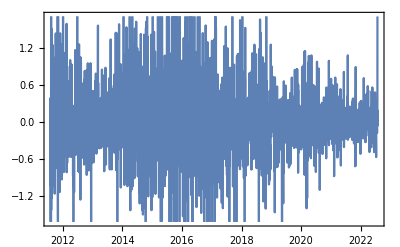

```mathematica
DateListPlot@doublefdseries
```

Compute the FractionalDTimeSeries of order 0.3531 (with default tol = 0.0001) to the original time series:

```mathematica
ts = FinancialData["TEVA","Close","Jan. 1, 2010"]
```

TimeSeries[…]

```mathematica
fdseries=FractionalDTimeSeries[ts, 0.3531]
```

TimeSeries[…]

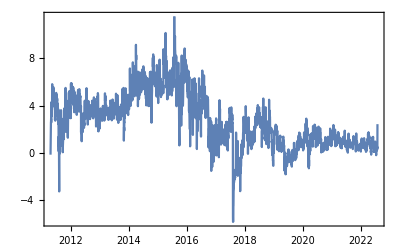

```mathematica
DateListPlot@fdseries
```

In the same time series, a FractionalDTimeSeries of order 0.3531 and tol = 0.01 will generate a differentiated time series with more data points:

```mathematica
fdseries=FractionalDTimeSeries[ts, 0.3531, 0.01]
```

TimeSeries[…]

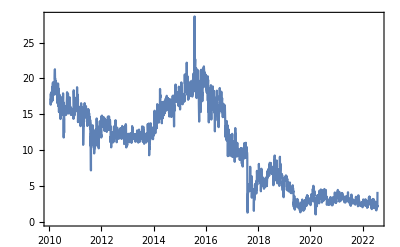

```mathematica
DateListPlot@fdseries
```

In contrast, a FractionalDTimeSeries of the same order 0.3531, but tol = 0.00001, will generate a differentiated time series with fewer data points:

```mathematica
fdseries=FractionalDTimeSeries[ts, 0.3531, 0.00001]
```

TimeSeries[…]

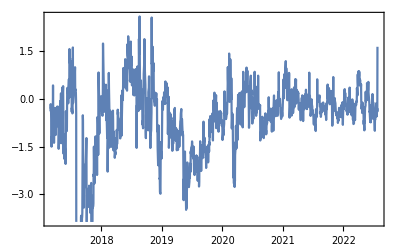

```mathematica
DateListPlot@fdseries
```

### Options

### Applications

Simulate an ARIMAProcess with linear trend, and apply a fractional differentiation of order 0.5 to it:

```mathematica
BlockRandom[SeedRandom[170];sample=RandomFunction[ARIMAProcess[{-0.1},1,{0.2},0.1],{1,1*^4}]]
```

TemporalData[…]

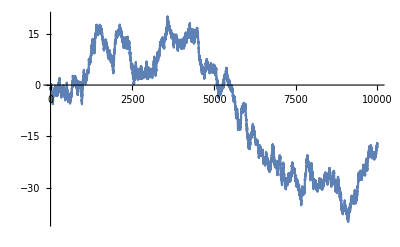
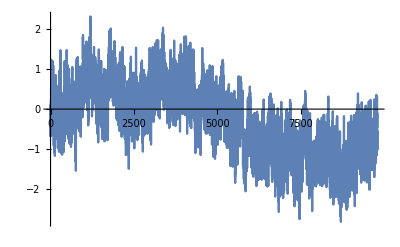

```mathematica
{ListLinePlot[sample],ListLinePlot[FractionalDTimeSeries[sample, 0.5]["Values"]]}
```

Simulate an FractionalBrownianMotionProcess with Hurst index 0.65, and apply a fractional differentiation of order 0.45 to it:

```mathematica
BlockRandom[SeedRandom[150];sample=RandomFunction[FractionalBrownianMotionProcess[0.65],{0,100,0.01}]]
```

TemporalData[…]

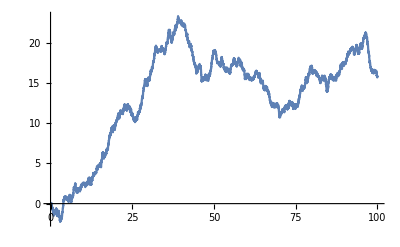
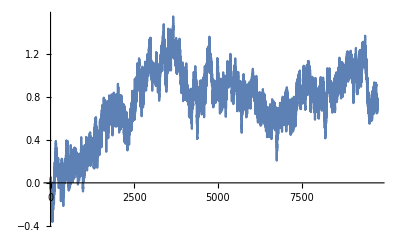

```mathematica
{ListLinePlot[sample],ListLinePlot[FractionalDTimeSeries[sample, 0.45]["Values"]]}
```

Get a time series of the word "Peru" using WordFrequencyData, and apply a fractional differentiation of order 0.35 and tol = 0.01 to it:

```mathematica
sample=WordFrequencyData["Peru", "TimeSeries"]
```

TimeSeries[…]

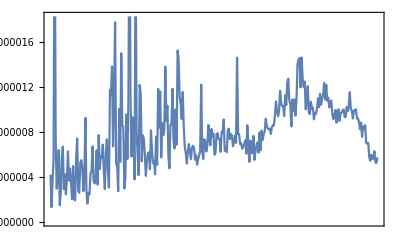
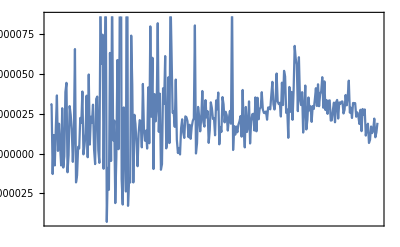

```mathematica
{DateListPlot[sample],DateListPlot[FractionalDTimeSeries[sample, 0.35, 0.01]]}
```

### Properties and Relations

### Possible Issues

FractionalDTimeSeries requires the order to be a positive real number. Negative orders (integration) are currently not implemented:

```mathematica
FractionalDTimeSeries[FinancialData["F","Close","Jan. 1, 2000"], -0.5]
```

FractionalDTimeSeries[TimeSeries[…],-0.5]

FractionalDTimeSeries requires the tolerance to be positive:

```mathematica
FractionalDTimeSeries[FinancialData["F","Close","Jan. 1, 2000"], 0.5, -0.0001]
```

FractionalDTimeSeries[TimeSeries[…],0.5,-0.0001]

If the tolerance is too small, no transformation will be performed:

```mathematica
FractionalDTimeSeries[FinancialData["F","Close","Jan. 1, 2000"], 0.5, 0.0000001]
```

ResourceFunction::usermessage: FractionalDTimeSeries

FractionalDTimeSeries[TimeSeries[…],0.5,1.×10^-7]

If the tolerance is set too high, the transformed time series will be essentially the same as the original one, but in a different scale:

```mathematica
ts=FinancialData["F","Close","Jan. 1, 2000"];
fdshightol=FractionalDTimeSeries[ts, 0.5, 0.15]
```

TimeSeries[…]

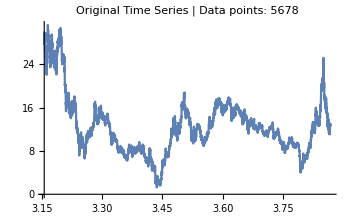
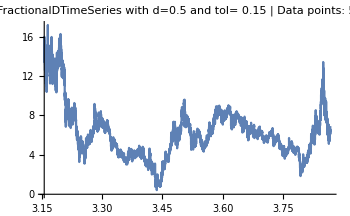

```mathematica
Row[
{ListLinePlot[ts,ImageSize->350,PlotLabel->Style["Original Time Series | Data points: "<>ToString@(Length@(ts["Values"])),Darker@Black, 10, Bold]], ListLinePlot[fdshightol,ImageSize->350,PlotLabel->Style["FractionalDTimeSeries with d=0.5 and tol= 0.15 | Data points: "<>ToString@(Length@(fdshightol["Values"])),
Darker@Black, 10, Bold]]}]
```

### Neat Examples

A logarithmically-transformed time series:

```mathematica
ts = Log@QuantityMagnitude@FinancialData["GE","Close","Jan. 1, 2000"]
```

TimeSeries[…]

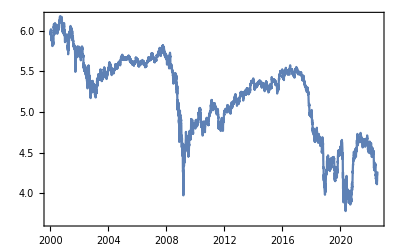

```mathematica
DateListPlot@ts
```

Find the relationship between the statistical value of a UnitRootTest and the CorrelationFunction of a transformed time series, by defining several values for d* between 0 and 1, and using them as the order of differentiation:

```mathematica
baseDs=Range[0,1,0.005];
setFSeries=Table[{d, FractionalDTimeSeries[ts,d]}, {d, baseDs}];
```

Apply a UnitRootTest (red axis) on each differentiated time series to see up from which level of d is possible to reject H_0. Also, compute its CorrelationFunction at lag 1 (blue axis) to compare:

```mathematica
statACFDataPlot={#[[1]],CorrelationFunction[#[[2]],1],UnitRootTest@#[[2]]}&/@setFSeries;
```

Plot the results:

```mathematica
corrPlot=ListLinePlot[
{#[[1]], #[[2]]}&/@statACFDataPlot,ImagePadding->{{50,50},{45,2}},
PlotStyle->Blue,Frame->{True,True,False,False},
FrameStyle->{Automatic,Blue,Automatic,Automatic},  
FrameTicks->{None,All,None,None},
PlotLabel->Style["Autocorrelation vs UnitRootTest P-value | NYSE:GE Time Series",Black, 13, Bold],
FrameLabel->{{Style["AC(1)", Bold],None},{Style["d*", 11,Bold],None}},
ImageSize->500];
statPlot=ListLinePlot[
{#[[1]], #[[3]]}&/@statACFDataPlot,ImagePadding->{{50,50},{45,2}},
PlotStyle->Red,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},
FrameStyle->{Automatic,Automatic,Automatic,Red},
FrameLabel->{{None,Style["STAT", Bold]},{None,None}},
PlotLabel->Style[" "],
ImageSize->500,
GridLines->{None,{0.05}},
GridLinesStyle->Directive[AbsoluteThickness[3/2],Red, Dashed],
Epilog->{Text[Style["Possible to reject H0 (pval<0.05)",9, Bold],Scaled[{0.015,0.125}],{-1,0}]}
];
```

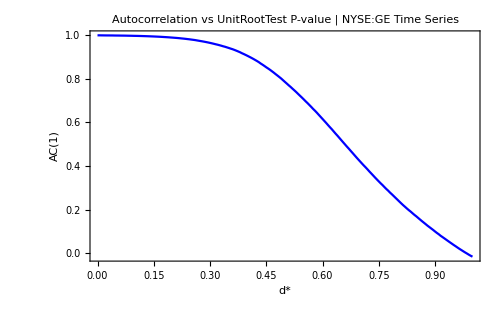
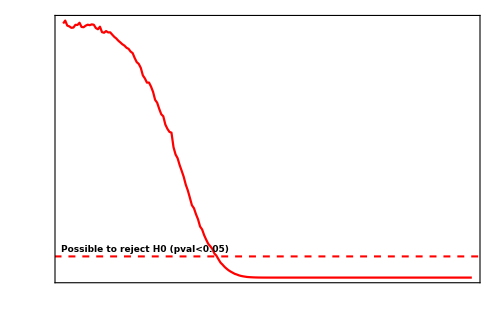

```mathematica
Overlay[{corrPlot,statPlot}]
```

## Source & Additional Information

### Contributed By

Frank Salvador Ygnacio Rosas

### Keywords

Fractional calculus

Fractional differentiation

Time series

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FractionalD

ItoProcess

TimeSeries

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Lopez de Prado, M. (2018). Advances in Financial Machine Learning. Wiley, New Jersey, 75-88.

Walasek, R. and Gajda, J. (2021). "Fractional differentiation and its use in machine learning". International Journal of Advances in Engineering Sciences and Applied Mathematics, Vol.13, No. 3, pp. 270-277. DOI: 10.1007/s12572-021-00299-5

### Links

Wolfram Community - "Fractional Differentiation and fBm: a study of long-memory processes"

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.